纯匿名函数

在我们看过 Wolfram 语言的所有例子后，我们现在准备进入一个稍高的抽象层次，并学习纯函数(也称为纯匿名函数)这一非常重要的概念。

使用纯函数将让 Wolfram 语言的能力达到一个新的级别，同时也让我们以更简单、更优雅的方式重做一些我们以前做过的事情。

让我们从一个简单的例子开始。假设我们有一个图片列表，我们想对每张图片应用模糊效果，使用 /@ 可以轻松完成。

将 Blur 应用于列表中的每一张图片：

```mathematica
Blur/@{-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-}

但现在如果我们想在 Blur 中包含参数 5。我们怎样才能做到这一点呢？答案是使用一个纯函数。

通过引入一个纯函数来包含一个参数：

```mathematica
Blur[#,5]&/@{-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-}

使用纯函数编写原先的模糊效果：

```mathematica
Blur[#]&/@{-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-}

# 是一个“槽”，每个元素都会被放进去。& 表示在它前面的是一个纯函数。

这里是与 Blur[#,5]&/@... 等价的展开形式：

```mathematica
{Blur[-Graphics-,5],Blur[-Graphics-,5],Blur[-Graphics-,5]}
```

{-Graphics-,-Graphics-,-Graphics-}

让我们来看一些其他的例子。每一次应用纯函数时，槽都会指明将每个元素放在哪里。

将每个字符串旋转 90°：

```mathematica
Rotate[#,90Degree]&/@{"one","two","three"}
```

{one,two,three}

将一个字符串旋转不同的角度：

```mathematica
Rotate["hello",#]&/@{30°,90°,180°,220°}
```

{hello,hello,hello,hello}

将文本显示为一系列不同的颜色：

```mathematica
Style["hello",20,#]&/@{Red,Orange,Blue,Purple}
```

{hello,hello,hello,hello}

创建不同大小的圆：

```mathematica
Graphics[Circle[ ],ImageSize->#]&/@{20,40,30,50,10}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

显示带边框的一列颜色及其相反色：

```mathematica
Framed[Column[{#,ColorNegate[#]}]]&/@{Red,Green,Blue,Purple,Orange}
```

{RGBColor[1, 0, 0]
RGBColor[0., 1., 1.],RGBColor[0, 1, 0]
RGBColor[1., 0., 1.],RGBColor[0, 0, 1]
RGBColor[1., 1., 0.],RGBColor[0.5, 0, 0.5]
RGBColor[0.5, 1., 0.5],RGBColor[1, 0.5, 0]
RGBColor[0., 0.5, 1.]}

计算维基百科三篇文章的长度：

```mathematica
StringLength[WikipediaData[#]]&/@{"apple","peach","pear"}
```

{31045,24153,11115}

将主题与结果配对：

```mathematica
{#,StringLength[WikipediaData[#]]}&/@{"apple","peach","pear"}
```

{{apple,31045},{peach,24153},{pear,11115}}

把所有东西做成一个表格：

```mathematica
Grid[{#,StringLength[WikipediaData[#]]}&/@{"apple","peach","pear"}]
```

apple | 31045
peach | 24153
pear | 11115

创建一个数字列表，然后在其上映射一个纯函数：

```mathematica
Style[#,Hue[#/10],5*#]&/@IntegerDigits[2^100]
```

{1,2,6,7,6,5,0,6,0,0,2,2,8,2,2,9,4,0,1,4,9,6,7,0,3,2,0,5,3,7,6}

下面是这个纯函数如果映射到 {6,8,9} 上会做什么：

```mathematica
{Style[6,Hue[6/10],5*6],Style[8,Hue[8/10],5*8],Style[9,Hue[9/10],5*9]}
```

{6,8,9}

现在我们已经看过了一些纯函数的实例，让我们更抽象地看看究竟发生了什么。

这是一个抽象的纯函数在一个列表上的映射：

```mathematica
f[#,x]&/@{a,b,c,d,e}
```

{f[a,x],f[b,x],f[c,x],f[d,x],f[e,x]}

这里是一个最简单的例子：

```mathematica
f[#]&/@{a,b,c,d,e}
```

{f[a],f[b],f[c],f[d],f[e]}

它等价于：

```mathematica
f/@{a,b,c,d,e}
```

{f[a],f[b],f[c],f[d],f[e]}

我们可以把槽放在纯函数中任何我们想放的位置，想放多少次就放多少次。所有的槽都将被应用于纯函数的任何对象所填充。

应用一个稍微复杂一些的纯函数：

```mathematica
f[#,{x,#},{#,#}]&/@{a,b,c}
```

{f[a,{x,a},{a,a}],f[b,{x,b},{b,b}],f[c,{x,c},{c,c}]}

列的形式更易于阅读：

```mathematica
f[#,{x,#},{#,#}]&/@{a,b,c}//Column
```

f[a,{x,a},{a,a}]
f[b,{x,b},{b,b}]
f[c,{x,c},{c,c}]

好了，现在我们终于可以讨论纯函数的真正工作原理了。当我们写下 f[x]时，我们是将函数 f 应用于 x。通常我们会使用一个特定的命名函数来代替 f，比如 Blur，所以我们有了 Blur[x]，等等。

但问题是，我们也可以用一个纯函数来代替 f。然后，无论我们将其应用于什么，都会被用来填充纯函数中的槽。

将纯函数应用于 x，因此 # 槽被填充为 x：

```mathematica
f[#,a]&  [x]
```

f[x,a]

相等的形式，用 @ 来代替[ ... ]：

```mathematica
f[#,a]& @ x
```

f[x,a]

所以现在我们可以看到 /@ 在做什么了：它只是将纯函数应用于列表中的每个元素。

```mathematica
f[#,a]&/@{x,y,z}
```

{f[x,a],f[y,a],f[z,a]}

同样的事情，写得更清楚一些：

```mathematica
{f[#,a]& @ x, f[#,a]& @ y, f[#,a]& @ z}
```

{f[x,a],f[y,a],f[z,a]}

为什么这很有用？首先，因为它是纯函数利用 /@ 来做所有事情的基础。但实际上，它本身也是很有用的，例如，作为一种避免重复的方法。

下面是一个涉及三个 # 出现的纯函数的例子。

将纯函数应用于 Blend[{Red,Yellow}]：

```mathematica
Column[{#,ColorNegate[#],#}]& [Blend[{Red,Yellow}]]
```

RGBColor[1, Rational[1, 2], 0]
RGBColor[0., 0.5, 1.]
RGBColor[1, Rational[1, 2], 0]

这是在不使用纯函数的情况下的样子：

```mathematica
Column[{Blend[{Red,Yellow}],ColorNegate[Blend[{Red,Yellow}]],Blend[{Red,Yellow}]}]
```

RGBColor[1, Rational[1, 2], 0]
RGBColor[0., 0.5, 1.]
RGBColor[1, Rational[1, 2], 0]

在 Wolfram 语言中，纯函数的工作方式与其他任何东西一样。虽然，就其本身而言，它并不完成任何具体的事情。

单独输入一个纯函数，它就会原原本本地返回：

```mathematica
f[#,2]&
```

f[#1,2]&

不过，把它交给函数 Map (/@)，它就会被用来做计算。

Map 使用纯函数来进行计算：

```mathematica
Map[f[#,2]&,{a,b,c,d,e}]
```

{f[a,2],f[b,2],f[c,2],f[d,2],f[e,2]}

在接下来的几节中，我们将看到越来越多的纯函数的应用。

词汇

code& |   | 纯函数
# |   | 纯函数中的槽

"共有 8 道习题"
"以及 1 道附加题" | "开始练习 »"

使用 Range 和一个纯函数来创建前 20 个数字的平方的列表。»

| 期望输出： |  
  | {1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400} |

把黄色、绿色和蓝色与红色混合的结果列出来。»

| 期望输出： |  
  | {RGBColor[1, Rational[1, 2], 0],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[Rational[1, 2], 0, Rational[1, 2]]} |

生成一个包含每个字母的大写和小写版本的带边框的列的列表。»

| 期望输出： |  
  | {"A"
"a","B"
"b","C"
"c","D"
"d","E"
"e","F"
"f","G"
"g","H"
"h","I"
"i","J"
"j","K"
"k","L"
"l","M"
"m","N"
"n","O"
"o","P"
"p","Q"
"q","R"
"r","S"
"s","T"
"t","U"
"u","V"
"v","W"
"w","X"
"x","Y"
"y","Z"
"z"} |

创建一个字母表，使用随机的颜色，以及随机背景颜色的边框。»

| 期望输出示例： |  
  | {"a","b","c","d","e","f","g","h","i","j","k","l","m","n","o","p","q","r","s","t","u","v","w","x","y","z"} |

将五国集团(G5)的国家及其国旗制成表格，并将结果排列在一个带完整边框的网格中。»






| 期望输出： |  
  | "France" | -Graphics-
"Germany" | -Graphics-
"Japan" | -Graphics-
"United Kingdom" | -Graphics-
"United States" | -Graphics- |

为维基百科上关于苹果、桃子和梨的文章创建一个词云列表。»

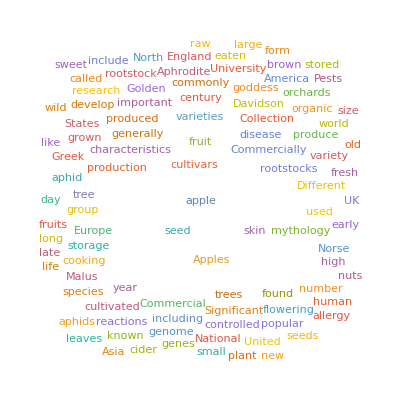
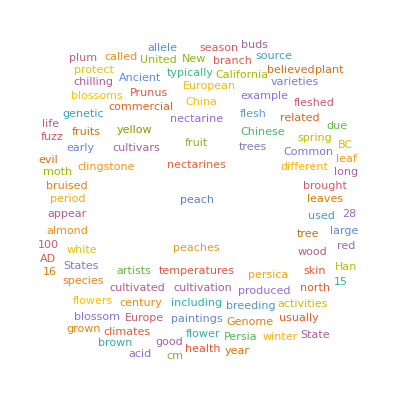
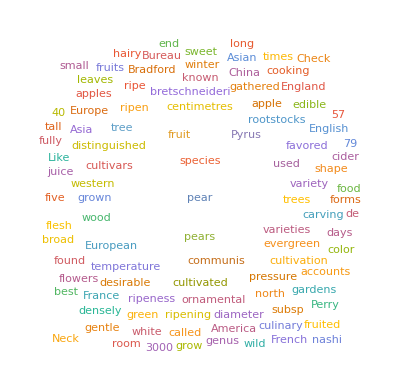
| 期望输出示例： |  
  | {-Graphics-,-Graphics-,-Graphics-} |

为维基百科上关于苹果、桃子和梨子的文章中的单词长度创建直方图列表。»

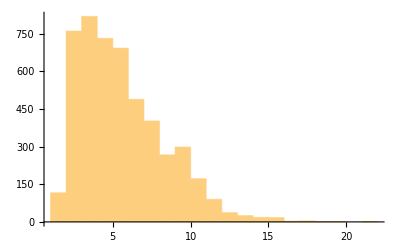
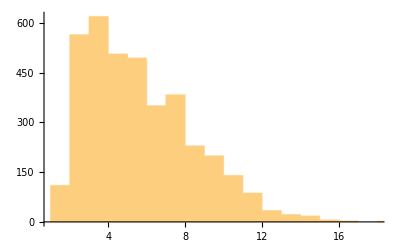
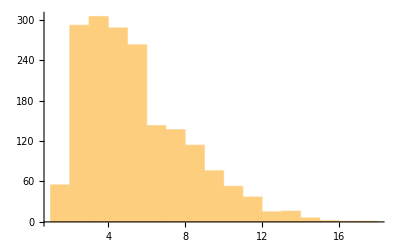
| 期望输出示例： |  
  | {-Graphics-,-Graphics-,-Graphics-} |

创建中美洲的地图列表，依次高亮每个国家。»

| 期望输出： |  
  | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-} |

给出 (#^2+1&)/@Range[10] 的更简单的形式。»

| 期望输出： |  
  | {2,5,10,17,26,37,50,65,82,101} |

问&答

为什么把它们称为“纯函数”？

因为它们只是作为可以应用参数的函数。它们有时也被称为匿名函数，因为与 Blur 这样的函数不同，它们没有名字。在这里，我称它们为“纯匿名函数”，以表达这两方面的意思。

为什么需要 &？

The & (ampersand) 表示在它之前的是纯函数的“体”，而不是函数的名字。f/@{1,2,3} 将得到 {f[1],f[2],f[3]}，而 f&/@{1,2,3} 则得到 {f,f,f}。

f[#,1]& 被解释为什么？

Function[f[#,1]]。这里的 Function 有时也被称为“函数的函数”。

技术笔记

纯函数是函数式编程的一个特点。它们通常被称为 lambda 表达式，因为它们在 20 世纪 30 年代被用于数学逻辑。令人困惑的是，“纯函数”一词有时只是指一个没有副作用的函数(即不给变量赋值，等等)。

Table[f[x],{x,{a,b,c}}] 实际上与 f/@{a,b,c} 的作用相同。它有时很有用，特别是在不想解释纯函数的情况下。

如果你在一个表达式中有多个嵌套的 &，那就要小心了！有时你可能需要插入括号。有时你可能不得不使用 Function 与一个命名的变量，比如 Function[x,x^2] 而不是 #^2&，以避免在不同函数中使用 # 的冲突。

有时，将 Function[x,x^2] 写成 x↦x^2 会使代码更美观。↦ 可以使用 \ [Function] 或者escfnesc 来输入。像 x ↦x^2 这样的形式与“x 被映射到 x^2”或“x 将成为 x^2”的标准数学符号是吻合的。

选项通常可以是纯函数。重要的是在整个纯函数周围加上括号，比如 ColorFunction→(Hue[#/4]&)，否则它不会被解释为你所期望的。

探索更多

Wolfram 语言中的函数式编程指南 »